```mathematica
Clear[R, V, S, ϵ,p];
```

```mathematica
Eigenvalues[{{-R0*V-ϵ,-R0*S,-R1*S},{R0*V,R0*S-γ,0},{0,0,R1*S-1}}]
```

{-1+R1 S,1/2 (R0 S-R0 V-γ-ϵ-√((-R0 S+R0 V+γ+ϵ)^2-4 (R0 V γ-R0 S ϵ+γ ϵ))),1/2 (R0 S-R0 V-γ-ϵ+√((-R0 S+R0 V+γ+ϵ)^2-4 (R0 V γ-R0 S ϵ+γ ϵ)))}

```mathematica
Simplify[1/2 (-1-epsilon-ⅈ R+R S-R V+√((-1-epsilon-ⅈ R+R S-R V)^2+4 (-epsilon-ⅈ R+epsilon R S-R V)))]
```

1/2 (-1-epsilon-ⅈ R+R S-R V+√(4 epsilon (-1+R S)-4 R (ⅈ+V)+(1+epsilon+R (ⅈ-S+V))^2))

```mathematica
FullSimplify[1/2 (-1-ϵ-ⅈ R+R S-R V+√((-1-ϵ-ⅈ R+R S-R V)^2+4 (-ϵ-ⅈ R+ϵ R S-R V)))]
```

1/4 (-1-epsilon-((-1+2 ⅈ)+epsilon) R-√(1+R (-2+4 p+R))-epsilon √(1+R (-2+4 p+R))+2 √(-4 epsilon-2 epsilon (-1+R)-4 ⅈ R-2 epsilon √((-1+R)^2+4 p R)+2 epsilon (1+R-√(1+R (-2+4 p+R)))+1/4 (1-(1-2 ⅈ) R+√(1+R (-2+4 p+R))+epsilon (1+R+√(1+R (-2+4 p+R))))^2))

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

0.

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

0.00120403

```mathematica
p=1
```

1

```mathematica
ϵ=11/9136
```

11/9136

```mathematica
R=4.5
```

4.5

```mathematica
Clear[R,epsilon]
```

```mathematica
FullSimplify[√((-1-epsilon-ⅈ R+R S-R V)^2+4 (-epsilon-ⅈ R+epsilon R S-R V))]
```

√(4 epsilon (-1+R S)-4 R (ⅈ+V)+(1+epsilon+R (ⅈ-S+V))^2)

```mathematica
Expand[(-1-epsilon-ⅈ R+R S-R V)^2]
```

1+2 epsilon+epsilon^2+2 ⅈ R+2 ⅈ epsilon R-R^2-2 R S-2 epsilon R S-2 ⅈ R^2 S+R^2 S^2+2 R V+2 epsilon R V+2 ⅈ R^2 V-2 R^2 S V+R^2 V^2

```mathematica
1+2 epsilon+epsilon^2+2 ⅈ R+2 ⅈ epsilon R-R^2-2 R S-2 epsilon R S-2 ⅈ R^2 S+R^2 S^2+2 R V+2 epsilon R V+2 ⅈ R^2 V-2 R^2 S V+R^2 V^2+4 (-epsilon-ⅈ R+epsilon R S-R V)
```

```mathematica
1+2 ϵ+ϵ^2+2 ⅈ R+2 ⅈ ϵ R-R^2-2 R S-2 ϵ R S-2 ⅈ R^2 S+R^2 S^2+2 R V+2 ϵ R V+2 ⅈ R^2 V-2 R^2 S V+R^2 V^2+(-4 ϵ-4 ⅈ R+4 ϵ R S-4 R V)
```

-20.2512-16.8324 ⅈ

```mathematica
"convert to exponential"-20.251221453050047-16.832393033250803 ⅈWith[{n=Abs[-20.251221453050047-16.832393033250803 ⅈ],a=Arg[-20.251221453050047-16.832393033250803 ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

26.3333 ⅇ^(ⅈ (-2.44813))

```mathematica
Expand[(-1-ϵ+R*S-R*V)]
```

-0.129734

```mathematica
1-2 R S+R^2 S^2+2 R V-2 R^2 S V+R^2 V^2+2 ϵ-2 R S ϵ+2 R V ϵ+ϵ^2
```

0.852758

```mathematica
√(26.33327601279994 ⅇ^(ⅈ (-2.448127046343737)))
```

1.74385-4.8262 ⅈ

```mathematica
I
```

ⅈ

```mathematica
(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)
```

(1-R (1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R)))+ϵ+1/2 ((-1+R) ϵ+√((-1+R)^2+4 p R) ϵ))^2-4 (ϵ-R (1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R))) ϵ+1/2 ((-1+R) ϵ+√((-1+R)^2+4 p R) ϵ))

```mathematica
f[x_]:=(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)
```

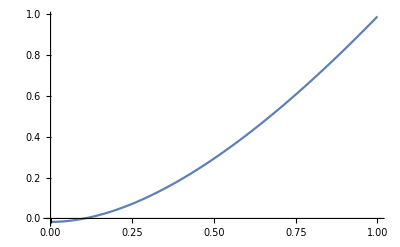

```mathematica
Plot[f[x],{p,0,1}]
```

```mathematica
g[x_]:=R V+ϵ-R S ϵ
```

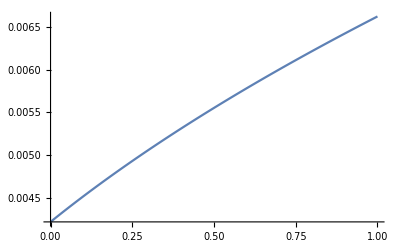

```mathematica
Plot[g[x],{p,0,1}]
```

```mathematica
g[p_]:=R V+ϵ-R S ϵ
```

```mathematica
Plot[g[p],{p,0,1}]
```

-Graphics-

```mathematica
g[x_]:R0 S-R0 V-γ-ϵ
```